```mathematica
(*animate solutions*)

σ=10;ρ=24.74;β=8/3; (*parameters*)
s=NDSolve[{Derivative[1][a][t]==-σ(a[t]-b[t]),Derivative[1][b][t]==-a[t] c[t]+ρ a[t]-b[t],Derivative[1][c][t]==a[t] b[t]-β c[t],a[0]==c[0]==0,b[0]==1},{a,b,c},{t,0,200},Method->"ExplicitRungeKutta"]; (*built in RK solver*)
s1 = a /. First@s; (*extracting components from list of interpolating functions that NDSolve returns*)
s2 = b /. First@s;
s3 = c /. First@s;
Animate[Show[{ParametricPlot3D[{s1[u],s2[u],s3[u]},{u,0,50},PlotPoints->1000,ColorFunction->"Aquamarine",PlotStyle->Thickness[.0025]],Graphics3D[{PointSize[0.025],Point[{s1[t],s2[t],s3[t]}]}]},PlotRange->All,BoxRatios->{1, 1, 1},BoxStyle->Dashed,Boxed->False,Axes->False,Ticks->None,ViewPoint->{-3,4,0}],{t,0,50},AnimationRate->1]
```

```mathematica
(*visualize RK4 solutions*)

SolveRK4[f1_,f2_,f3_,y0_,t_List]:=Module[{y,dt,k1,k2,k3,k4,l1,l2,l3,l4,m1,m2,m3,m4,a},y=ConstantArray[0.,{3,Length[t]}];
y[[1,1]]=y0[[1]]; (*initial conditions*)
y[[2,1]]=y0[[2]];
y[[3,1]]=y0[[3]];
dt=Abs[t[[2]]-t[[1]]];
For[a=1,a<Length[t],a++,k1=f1[y[[1,a]],y[[2,a]],y[[3,a]]];
l1=f2[y[[1,a]],y[[2,a]],y[[3,a]]]; (*first order coefficients*)
m1=f3[y[[1,a]],y[[2,a]],y[[3,a]]];
k2=f1[y[[1,a]]+0.5*k1*dt,y[[2,a]]+0.5*l1*dt,y[[3,a]]+0.5*m1*dt]; (*second order coefficients*)
l2=f2[y[[1,a]]+0.5*k1*dt,y[[2,a]]+0.5*l1*dt,y[[3,a]]+0.5*m1*dt];
m2=f3[y[[1,a]]+0.5*k1*dt,y[[2,a]]+0.5*l1*dt,y[[3,a]]+0.5*m1*dt];
k3=f1[y[[1,a]]+0.5*k2*dt,y[[2,a]]+0.5*l2*dt,y[[3,a]]+0.5*m2*dt];(*third order coefficients*)
l3=f2[y[[1,a]]+0.5*k2*dt,y[[2,a]]+0.5*l2*dt,y[[3,a]]+0.5*m2*dt];
m3=f3[y[[1,a]]+0.5*k2*dt,y[[2,a]]+0.5*l2*dt,y[[3,a]]+0.5*m2*dt];
k4=f1[y[[1,a]]+k3*dt,y[[2,a]]+l3*dt,y[[3,a]]+m3*dt];(*fourth order coefficients*)
l4=f2[y[[1,a]]+k3*dt,y[[2,a]]+l3*dt,y[[3,a]]+m3*dt];
m4=f3[y[[1,a]]+k3*dt,y[[2,a]]+l3*dt,y[[3,a]]+m3*dt];
y[[1,a+1]]=y[[1,a]]+(k1+2*k2+2*k3+k4)*dt/6;(*linear combinations of coefficients to get y_n*)
y[[2,a+1]]=y[[2,a]]+(l1+2*l2+2*l3+l4)*dt/6;
y[[3,a+1]]=y[[3,a]]+(m1+2*m2+2*m3+m4)*dt/6;];
y]

(*define system*)
f1[y1_,y2_,y3_]:=σ (y2-y1) (*lorenz equations*)
f2[y1_,y2_,y3_]:=y1 (ρ-y3)-y2
f3[y1_,y2_,y3_]:=y1 y2-β y3

y0={1,1,1}; (*initial conditions*)

tmax=30; (*t_final*)
dt=0.005; (*step size*)
tt=Range[0,tmax,dt]; (*time (list)*)
y=SolveRK4[f1,f2,f3,y0,tt]; (*run SolveRK4 and save result*)
ListLinePlot3D[Transpose[y],ColorFunction->"Aquamarine",PlotStyle->Thickness[.004],Boxed->True,BoxStyle->Directive[Dashed],BoxRatios->{1, 1, 1},Axes->False,Ticks->False,PlotRange->All,ViewPoint->{8,-3,0}]
```

-Graphics3D-

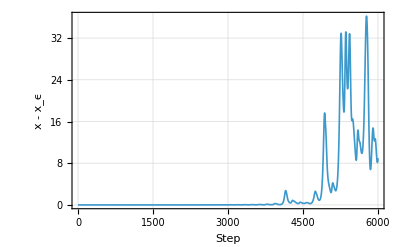

```mathematica
(*visualize difference between solutions*)

y01=y0+{0,0,0.001}; (*small difference in I.C.*)
y1=SolveRK4[f1,f2,f3,y01,tt]; 
y=SolveRK4[f1,f2,f3,y0,tt];
difs=Abs[Map[Norm,Transpose[y]-Transpose[y1]]];
ListLinePlot[difs,PlotRange->All,PlotTheme->"Detailed",PlotStyle->Thickness[.003],FrameLabel->{"Step",Text@Style["x - \!\(\*SubscriptBox[\(x\), \(ϵ\)]\)", Bold]}]
```